```mathematica
ClearAll["Global`*"]
Import["https://qtechtheory.org/questlink.m"]
CreateDownloadedQuESTEnv[]
```

LinkObject[…]

## Parameters

```mathematica
numQb=4;
PI=N[π,12];
```

## QC

```mathematica
ψIN=CreateQureg[numQb];
ψOUT=CreateQureg[numQb];
ψWP=CreateQureg[numQb];
```

## Circuit

```mathematica
circXY[i_,j_,θ_]:=(
circ={Subscript[Rz, i][π/2],Subscript[H, j],Subscript[C, j][Subscript[X, i]],Subscript[Rz, i][-π/2],Subscript[Rz, j][π/2],Subscript[H, i],Subscript[H, j],Subscript[Rz, i][θ/2],Subscript[Rz, j][-θ/2],Subscript[Rz, i][PI/2],Subscript[H, j],Subscript[C, j][Subscript[X, i]],Subscript[Rz, i][-π/2],Subscript[Rz, j][π/2],Subscript[H, i],Subscript[H, j]};
Return[circ]
)
```

## Plot

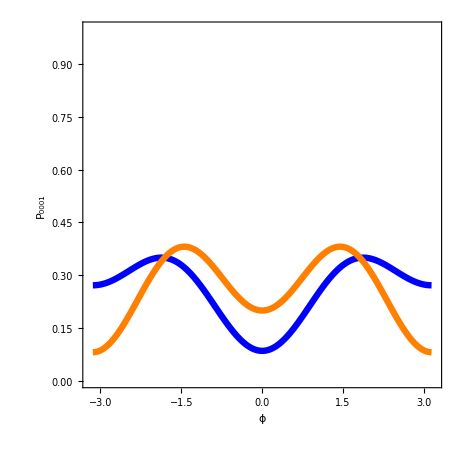

```mathematica
Nϕ=201;
dϕ=2 PI/(Nϕ-1);
θ1=PI/1.5;
θ2=PI/1.5;
α=π/4;
Pro1=Table[(
ϕ=-PI+(iϕ-1)*dϕ;
circθ=Join[circXY[0,1,θ1],circXY[1,2,θ2],circXY[2,3,θ1]];
circϕ={Subscript[Rz, 0][ϕ],Subscript[Rz, 1][α],Subscript[Rz, 2][-α],Subscript[Rz, 3][ϕ]};
circ=Join[{Subscript[X, 0]},circθ,circϕ,circθ,circϕ,circθ];
ApplyCircuit[ψIN,circ,ψOUT];
OUT=GetQuregMatrix[ψOUT];
Zave=CalcExpecPauliString[ψOUT,Subscript[Z, numQb-1],ψWP];
Pz=(1-Zave)/2;
{ϕ,Pz}
),{iϕ,Nϕ}];

α=-π/1.5;
Pro2=Table[(
ϕ=-PI+(iϕ-1)*dϕ;
circθ=Join[circXY[0,1,θ1],circXY[1,2,θ2],circXY[2,3,θ1]];
circϕ={Subscript[Rz, 0][ϕ],Subscript[Rz, 1][α],Subscript[Rz, 2][-α],Subscript[Rz, 3][ϕ]};
circ=Join[{Subscript[X, 0]},circθ,circϕ,circθ,circϕ,circθ];
ApplyCircuit[ψIN,circ,ψOUT];
OUT=GetQuregMatrix[ψOUT];
Zave=CalcExpecPauliString[ψOUT,Subscript[Z, numQb-1],ψWP];
Pz=(1-Zave)/2;
{ϕ,Pz}
),{iϕ,Nϕ}];
plot1=ListLinePlot[Pro1,PlotStyle->{Blue,Thickness[0.01]},PlotRange->{{-3.2,3.2},{0,1}},Axes->Automatic(*{False,False}*),Frame->True,FrameLabel->{"ϕ","P_0001"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->{460,460},LabelStyle->{FontSize->18}];
plot2=ListLinePlot[Pro2,PlotStyle->{Orange,Thickness[0.01]},PlotRange->{{-3.2,3.2},{0,1}},Axes->Automatic(*{False,False}*),Frame->True,FrameLabel->{"ϕ","P_0001"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->{460,460},LabelStyle->{FontSize->18}];
Show[plot1,plot2,AspectRatio->1]
```